```mathematica
ex=100*ReadList["~/excluidas.txt"];
```

```mathematica
exbc=BinCounts[ex,{1,100,1}]
```

{24,30,24,34,35,50,59,59,67,81,74,93,70,97,106,81,106,99,82,92,86,89,80,99,94,95,111,89,100,118,91,79,100,88,102,60,72,73,59,70,53,54,48,67,46,49,52,36,36,35,28,31,25,31,25,31,16,20,21,20,11,13,18,9,9,20,16,15,9,8,7,2,5,5,10,2,4,4,4,5,6,4,0,1,7,5,3,8,4,6,3,2,2,2,4,5,16,11,3}

```mathematica
Total[exbc]
```

4110

```mathematica
exarea=1*Total[exbc]
```

4110

```mathematica
exmax=Max[exbc/exarea]
```

59/2055

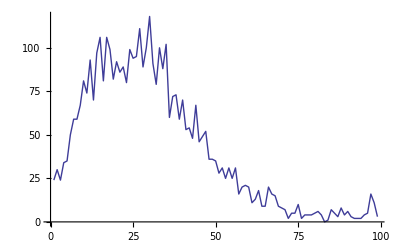

```mathematica
exfig=ListPlot[exbc,Joined->True]
```

```mathematica
in=100*ReadList["~/incluidas.txt"];
```

```mathematica
inbc=BinCounts[in,{1,100,0.5}]
```

{9,14,21,11,15,27,32,35,29,40,58,57,63,59,87,75,85,90,131,120,131,138,178,179,188,196,216,219,244,230,227,246,282,271,240,260,275,241,276,286,274,249,306,302,289,307,313,277,351,312,312,302,337,331,326,353,365,348,353,337,354,304,338,325,289,317,288,310,278,273,332,292,300,313,316,319,338,282,268,260,275,273,261,239,234,230,255,236,220,216,223,237,190,240,217,205,229,172,199,173,165,143,187,173,160,143,162,145,135,100,136,120,127,121,100,114,106,104,114,80,97,91,82,71,72,85,69,67,54,77,49,60,67,59,58,49,52,60,53,45,53,50,48,44,43,41,41,37,38,33,24,32,26,34,28,32,34,38,32,41,32,29,29,34,34,33,36,24,31,24,28,29,26,42,23,30,20,28,27,20,24,24,21,7,4,7,9,7,2,3,0,0,0,0,0,0,0,0}

```mathematica
Max[inbc]
```

365

```mathematica
PlotLabel
```

```mathematica
Total[inbc]
```

27933

```mathematica
inarea=1/2*Total[inbc]
```

27933/2

```mathematica
areas={inarea,exarea}
```

{27933/2,4110}

```mathematica
inmax=Max[inbc/inarea]
```

730/27933

```mathematica
N[{exmax,inmax}]
```

{0.0287105,0.026134}

```mathematica
exmax*areas//N
```

{400.985,118.}

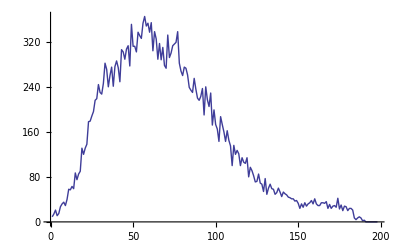

```mathematica
infig=ListPlot[inbc,Joined->True]
```

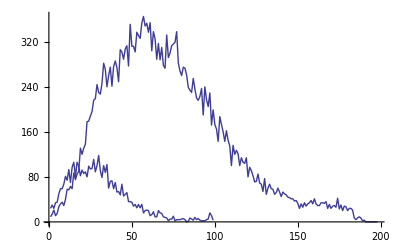

```mathematica
Show[exfig,infig,PlotRange->All]
```